```mathematica
Rz[θ_]:={{ⅇ^((-ⅈ θ)/2),0},{0,ⅇ^((ⅈ θ)/2)}}
Rx[θ_]:={{Cos[θ/2],-ⅈ Sin[θ/2]},{-ⅈ Sin[θ/2],Cos[θ/2]}}
Ry[θ_]:={{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}}
Z={{1,0},{0,-1}};
X={{0,1},{1,0}};
CNOT={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
CNOTac=({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 1, 0}});
SWAP={{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}};
Y={{0,-ⅈ},{ⅈ,0}};
H=1/(√2){{1,1},{1,-1}};
U[θ_,ϕ_,λ_]:={{ⅇ^(ⅈ ϕ)Cos[θ],-ⅇ^(-ⅈ λ)Sin[θ]},{ⅇ^(ⅈ λ)Sin[θ],ⅇ^(-ⅈ ϕ)Cos[θ]}}
YYt[t_]:=ⅇ^((ⅈ π t)/2){{Cos[(π t)/2],0,0,ⅈ Sin[(π t)/2]},{0,Cos[(π t)/2],-ⅈ Sin[(π t)/2],0},{0,-ⅈ Sin[(π t)/2],Cos[(π t)/2],0},{ⅈ Sin[(π t)/2],0,0,Cos[(π t)/2]}}
Xpow[t_]:=ⅇ^((ⅈ π t)/2){{Cos[π t],-ⅈ Sin[π t]},{-ⅈ Sin[π t],Cos[π t]}}
Zpow[t_]:={{1,0},{0,ⅇ^(ⅈ π t)}}
```

```mathematica
(X.({{1}, {-1}}))/(√2)
```

{{1/(√2)},{1/(√2)}}

```mathematica
ArrayFlatten[IdentityMatrix[4]⊗Ry[π/4]].ArrayFlatten[IdentityMatrix[2]⊗CNOT].ArrayFlatten[IdentityMatrix[4]⊗Ry[π/4]].CNOTac.ArrayFlatten[IdentityMatrix[4]⊗Ry[-π/4]].ArrayFlatten[IdentityMatrix[2]⊗CNOT].ArrayFlatten[IdentityMatrix[4]⊗Ry[-π/4]]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
Eigenvalues[J({{-Cos[k]+g, -ⅈ Sin[k]}, {ⅈ Sin[k], Cos[k]-g}})]
Eigenvalues[J({{-Cos[k]-g, -ⅈ Sin[k]}, {ⅈ Sin[k], Cos[k]+g}})]
```

{-J √(1+g^2-2 g Cos[k]),J √(1+g^2-2 g Cos[k])}

{-J √(1+g^2+2 g Cos[k]),J √(1+g^2+2 g Cos[k])}

```mathematica
f[J_,g_]:=NIntegrate[-J/π √(1+g^2+2 g Cos[k]),{k,0,π}]
```

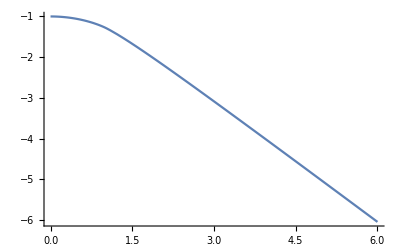

```mathematica
Plot[f[1,g],{g,0,6}]
```

```mathematica
ham=ArrayFlatten[Z⊗Z]+(ArrayFlatten[IdentityMatrix[2]⊗X]+ArrayFlatten[X⊗IdentityMatrix[2]]);
v={0,β,γ,0};
v*.ham.v
```

-β Conjugate[β]-γ Conjugate[γ]

```mathematica
ArrayFlatten[H⊗IdentityMatrix[2]].CNOT.{α,β,γ,δ}//MatrixForm
```

(α/(√2)+δ/(√2)
β/(√2)+γ/(√2)
α/(√2)-δ/(√2)
β/(√2)-γ/(√2))

```mathematica
ArrayFlatten[Zpow[1]⊗IdentityMatrix[2]].ArrayFlatten[Xpow[2]⊗IdentityMatrix[2]].YYt[3]
```

{{0,0,0,1},{0,0,-1,0},{0,1,0,0},{-1,0,0,0}}

```mathematica
ArrayFlatten[IdentityMatrix[2]⊗H].{α,δ,γ,β}//MatrixForm
```

(α/(√2)+δ/(√2)
α/(√2)-δ/(√2)
β/(√2)+γ/(√2)
-β/(√2)+γ/(√2))

```mathematica
ArrayFlatten[ArrayFlatten[CNOT⊗CNOT]⊗Z]//MatrixForm
```

```mathematica
SWAP.CNOT.SWAP//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

```mathematica
ArrayFlatten[Rx[γ]⊗Rx[δ]]//MatrixForm
```

(Cos[γ/2] Cos[δ/2] | -ⅈ Cos[γ/2] Sin[δ/2] | -ⅈ Cos[δ/2] Sin[γ/2] | -Sin[γ/2] Sin[δ/2]
-ⅈ Cos[γ/2] Sin[δ/2] | Cos[γ/2] Cos[δ/2] | -Sin[γ/2] Sin[δ/2] | -ⅈ Cos[δ/2] Sin[γ/2]
-ⅈ Cos[δ/2] Sin[γ/2] | -Sin[γ/2] Sin[δ/2] | Cos[γ/2] Cos[δ/2] | -ⅈ Cos[γ/2] Sin[δ/2]
-Sin[γ/2] Sin[δ/2] | -ⅈ Cos[δ/2] Sin[γ/2] | -ⅈ Cos[γ/2] Sin[δ/2] | Cos[γ/2] Cos[δ/2])